# Metastable states?

## Operators

```mathematica
Id = {{1, 0}, {0, 1}};
Sx= (1/2){{0, 1},{1, 0}};
Sy =(1/2){{0, -I},{I, 0}};
Sz = (1/2){{1, 0},{0, -1}};
```

```mathematica
MatrixForm[Sx]
```

(0 | 1/2
1/2 | 0)

```mathematica
MatrixForm[KroneckerProduct[Sx, Sx]+KroneckerProduct[Sy, Sy]+KroneckerProduct[Sz, Sz] -1/4KroneckerProduct[Id, Id]  ]
```

(0 | 0 | 0 | 0
0 | -1/2 | 1/2 | 0
0 | 1/2 | -1/2 | 0
0 | 0 | 0 | 0)

```mathematica
h = KroneckerProduct[Sx, Sx]+KroneckerProduct[Sy, Sy]+KroneckerProduct[Sz, Sz] -1/4KroneckerProduct[Id, Id];
```

Let consider one line segment with five sites

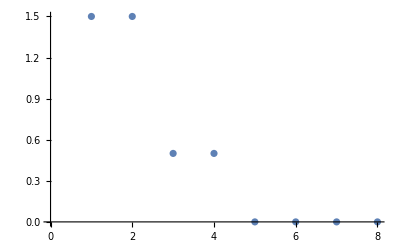

```mathematica
L=3;
H = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], h, IdentityMatrix[2^(L-1-k)]], {k, 1, L-1}];
ListPlot[Eigenvalues[-H]]
```

```mathematica
T = Table[t[k], {k, 1, 2^L}];
```

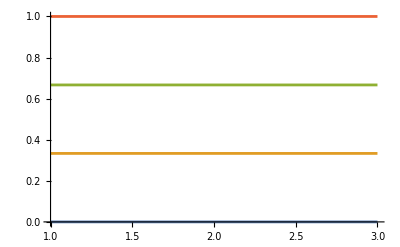

```mathematica
ListPlot[{T[[5]], T[[6]], T[[7]], T[[8]]}, Joined->True, PlotRange->{{1, L}, {0,1}}]
```

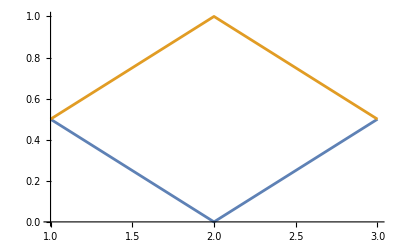

```mathematica
ListPlot[{T[[3]], T[[4]]}, Joined->True, PlotRange->{{1, L}, {0,1}}]
```

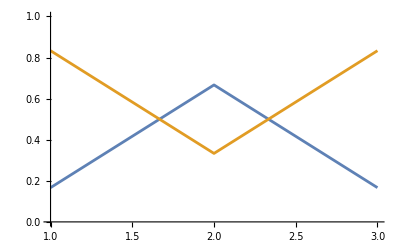

```mathematica
ListPlot[{T[[1]], T[[2]]}, Joined->True, PlotRange->{{1, L}, {0,1}}]
```

```mathematica
L=5;
```

```mathematica
H = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], h, IdentityMatrix[2^(L-1-k)]], {k, 1, L-1}];
```

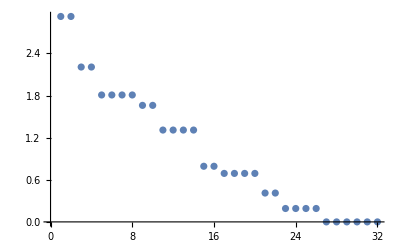

```mathematica
ListPlot[Eigenvalues[-H]]
```

I want to translate back to up-down states

```mathematica
Table[BaseForm[2^L-k, 2], {k ,1, 2^L}]
```

{11111_2,11110_2,11101_2,11100_2,11011_2,11010_2,11001_2,11000_2,10111_2,10110_2,10101_2,10100_2,10011_2,10010_2,10001_2,10000_2,1111_2,1110_2,1101_2,1100_2,1011_2,1010_2,1001_2,1000_2,111_2,110_2,101_2,100_2,11_2,10_2,1_2,0_2}

Probability of finding a spin at state x

```mathematica
vec[x_, L_]:= Table[If[EvenQ[Floor[k/2^(L-x)]], 1, 0], {k, 0, 2^L-1}]
```

```mathematica
vec[1,5]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
t[k_]:= Module[{Evec, norm, table, j},
Evec = Eigenvectors[H][[k]]//N;
norm = Norm[Evec]^2;
Evec= Evec^2;
table =Table[{j, N[Dot[Evec, vec[j, L]]/norm]}, {j, 1, L}];
Return[table]
]
```

```mathematica
t[1]
```

{{1,0.244167},{2,0.647235},{3,0.217197},{4,0.647235},{5,0.244167}}

```mathematica
T = Table[t[k], {k, 1, 2^L}];
```

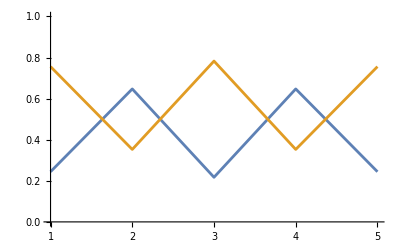

```mathematica
ListPlot[{T[[1]], T[[2]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

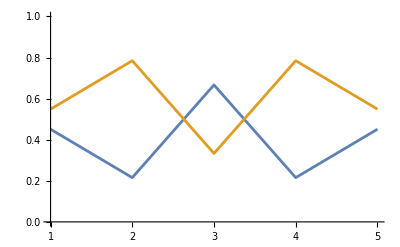

```mathematica
ListPlot[{T[[3]], T[[4]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

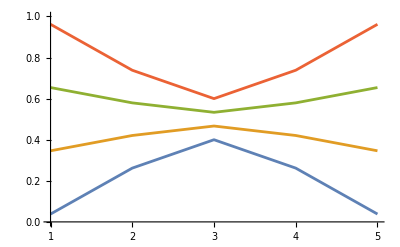

```mathematica
ListPlot[{T[[5]], T[[6]], T[[7]], T[[8]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

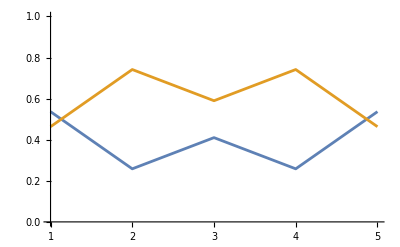

```mathematica
ListPlot[{T[[9]], T[[10]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

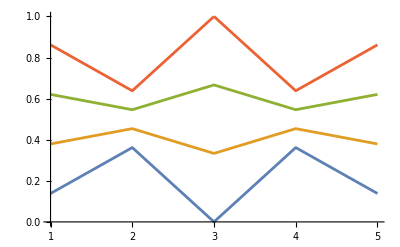

```mathematica
ListPlot[{T[[11]], T[[12]], T[[13]], T[[14]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

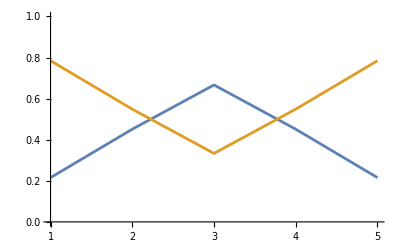

```mathematica
ListPlot[{T[[15]], T[[16]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

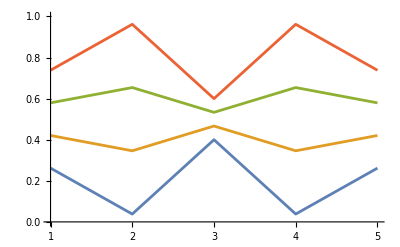

```mathematica
ListPlot[{T[[17]], T[[18]], T[[19]], T[[20]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

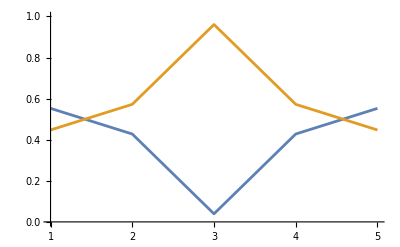

```mathematica
ListPlot[{T[[21]], T[[22]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

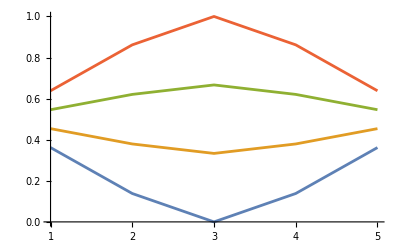

```mathematica
ListPlot[{T[[23]], T[[24]], T[[25]], T[[26]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

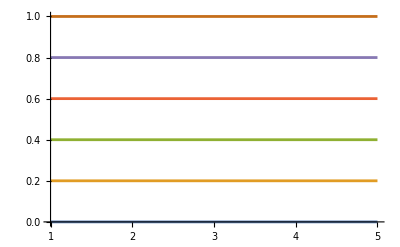

```mathematica
ListPlot[{T[[27]], T[[28]], T[[29]], T[[30]], T[[31]], T[[32]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

## Parallel lines L=3

Let’s do two parallel lines

```mathematica
M=6;
L=3;
```

```mathematica
H1 = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], h, IdentityMatrix[2^(M-k-1)]], {k, 1, L-1}] ;
```

```mathematica
H2 = Sum[KroneckerProduct[IdentityMatrix[2^(L +k-1)], h, IdentityMatrix[2^(L-k-1)]], {k, 1, L-1}] ;
```

```mathematica
H3x = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sx, IdentityMatrix[2^(L-1)], Sx, IdentityMatrix[2^(L-k)]], {k, 1, L}];
```

```mathematica
H3y = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sy, IdentityMatrix[2^(L-1)], Sy, IdentityMatrix[2^(L-k)]], {k, 1, L}];
```

```mathematica
H3z = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sz, IdentityMatrix[2^(L-1)], Sz, IdentityMatrix[2^(L-k)]], {k, 1, L}] - (L/4)IdentityMatrix[2^M];
```

```mathematica
Hp = -H1 - H2 + (1/10)(H3x + H3y  +H3z);
```

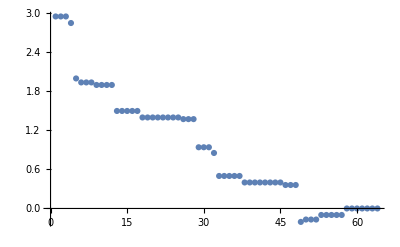

```mathematica
ListPlot[Eigenvalues[Hp]]
```

```mathematica
EVs =Eigenvectors[Hp];
```

```mathematica
tp[k_, evs_]:= Module[{Evec, norm, table, j},
Evec = evs[[k]]//N;
norm = Norm[Evec]^2;
Evec= Evec^2;
table =Table[{j, N[Dot[Evec, vec[j, M]]/norm]}, {j, 1, L}];
Return[table]
]
```

```mathematica
Tp = Table[tp[k, EVs], {k, 1, 2^M}];
```

```mathematica
Tp[[1]]
```

{{1,0.159973},{2,0.680054},{3,0.159973}}

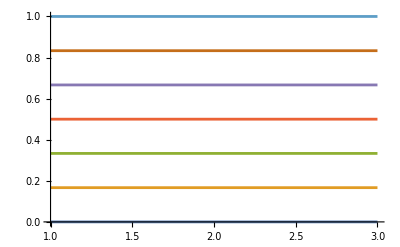

```mathematica
ListPlot[{Tp[[58]], Tp[[59]], Tp[[60]],Tp[[61]], Tp[[62]], Tp[[63]], Tp[[64]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

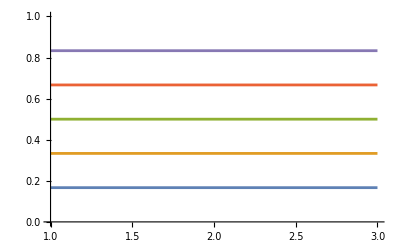

```mathematica
ListPlot[{Tp[[53]], Tp[[54]], Tp[[55]],Tp[[56]], Tp[[57]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

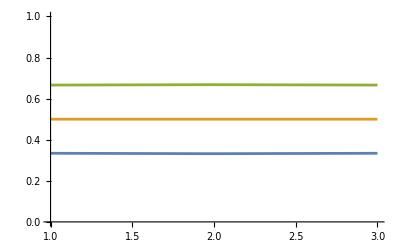

```mathematica
ListPlot[{Tp[[50]], Tp[[51]], Tp[[52]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

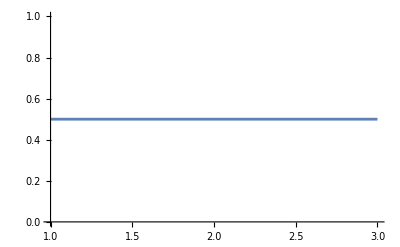

```mathematica
ListPlot[{Tp[[49]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

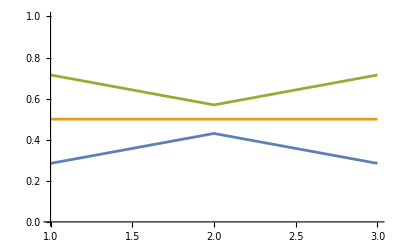

```mathematica
ListPlot[{Tp[[46]], Tp[[47]], Tp[[48]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

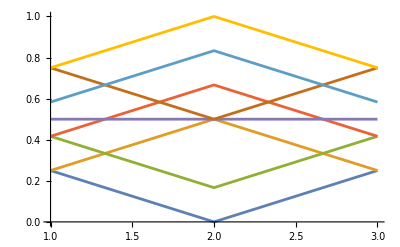

```mathematica
ListPlot[{Tp[[38]], Tp[[39]], Tp[[40]],Tp[[41]], Tp[[42]], Tp[[43]], Tp[[44]], Tp[[45]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

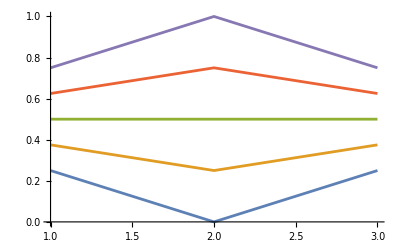

```mathematica
ListPlot[{Tp[[33]], Tp[[34]], Tp[[35]],Tp[[36]], Tp[[37]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

```mathematica
ListPlot[{Tp[[32]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

-Graphics-

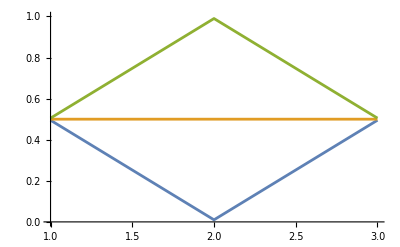

```mathematica
ListPlot[{Tp[[29]], Tp[[30]], Tp[[31]]}, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

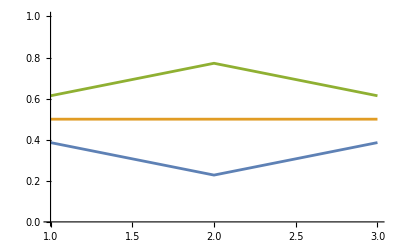

```mathematica
ListPlot[{Tp[[26]], Tp[[27]], Tp[[28]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

## Parallel lines L=4

Let’s do two parallel lines

```mathematica
M=8;
L=4;
```

```mathematica
H1 = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], h, IdentityMatrix[2^(M-k-1)]], {k, 1, L-1}] ;
```

```mathematica
H2 = Sum[KroneckerProduct[IdentityMatrix[2^(L +k-1)], h, IdentityMatrix[2^(L-k-1)]], {k, 1, L-1}] ;
```

```mathematica
H3x = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sx, IdentityMatrix[2^(L-1)], Sx, IdentityMatrix[2^(L-k)]], {k, 1, L}];
```

```mathematica
H3y = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sy, IdentityMatrix[2^(L-1)], Sy, IdentityMatrix[2^(L-k)]], {k, 1, L}];
```

```mathematica
H3z = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sz, IdentityMatrix[2^(L-1)], Sz, IdentityMatrix[2^(L-k)]], {k, 1, L}] - (L/4)IdentityMatrix[2^M];
```

```mathematica
Hp = -H1 - H2 + (1/10)(H3x + H3y  +H3z);
```

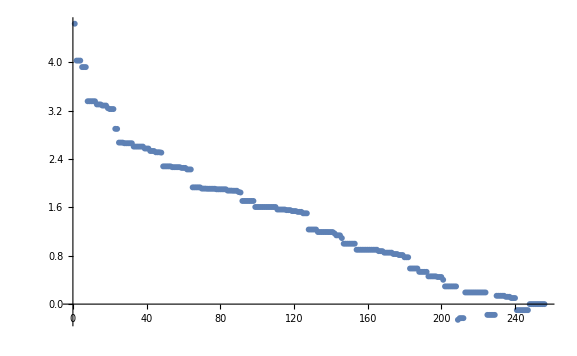

```mathematica
ListPlot[Eigenvalues[Hp]]
```

```mathematica
EVs =Eigenvectors[Hp];
```

```mathematica
tp[k_, evs_]:= Module[{Evec, norm, table, j},
Evec = evs[[k]]//N;
norm = Norm[Evec]^2;
Evec= Evec^2;
table =Table[{j, N[Dot[Evec, vec[j, M]]/norm]}, {j, 1, L}];
Return[table]
]
```

```mathematica
Tp = Table[tp[k, EVs], {k, 1, 2^M}];
```

General::munfl: 1.14204×10^-79 2.18165×10^-288 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.77277×10^-225 8.23469×10^-192 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.39508×10^-214 4.67109×10^-110 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^1. encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Tp[[209]]
```

{{1,0.5},{2,0.5},{3,0.5},{4,0.5}}

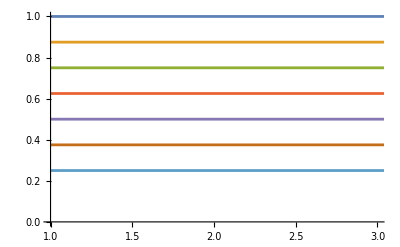

```mathematica
ListPlot[{Tp[[256]], Tp[[255]], Tp[[254]],Tp[[253]], Tp[[252]], Tp[[251]], Tp[[250]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

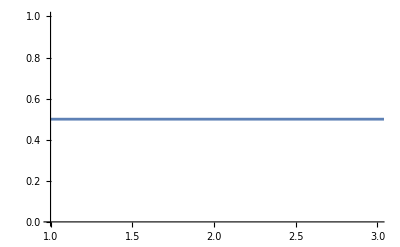

```mathematica
ListPlot[{Tp[[209]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

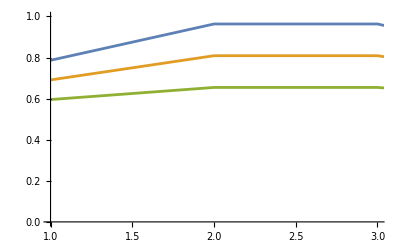

```mathematica
ListPlot[{Tp[[208]], Tp[[207]], Tp[[206]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

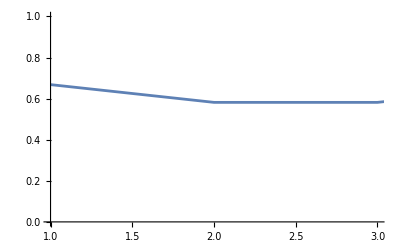

```mathematica
ListPlot[{Tp[[237]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

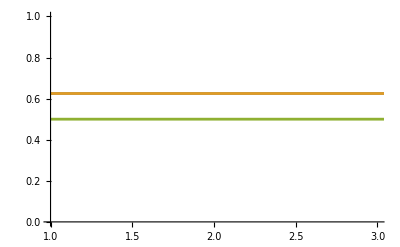

```mathematica
ListPlot[{Tp[[162]], Tp[[161]], Tp[[160]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

```mathematica
ListPlot[{Tp[[38]], Tp[[39]], Tp[[40]],Tp[[41]], Tp[[42]], Tp[[43]], Tp[[44]], Tp[[45]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

-Graphics-

```mathematica
ListPlot[{Tp[[33]], Tp[[34]], Tp[[35]],Tp[[36]], Tp[[37]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

-Graphics-

```mathematica
ListPlot[{Tp[[100]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

-Graphics-

```mathematica
ListPlot[{Tp[[29]], Tp[[30]], Tp[[31]]}, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

-Graphics-

```mathematica
ListPlot[{Tp[[26]], Tp[[27]], Tp[[28]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

-Graphics-